# 完整示例

```mathematica
(* 这是一系列中文视频教程：Mathematica实用入门的学习笔记第二部分 *)
```

```mathematica
data1 = Table[x^2, {x, 1, 20}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

## 绘制图线

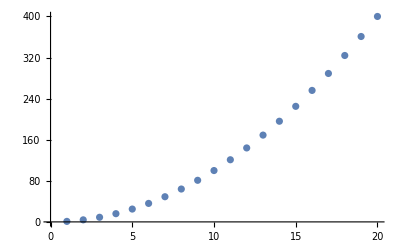

```mathematica
lpdata1 = ListPlot[data1]
```

## 拟合数据

```mathematica
fitdata1 = Fit[data1,{1,x},x]
```

21. x-77.

## 绘制拟合曲线

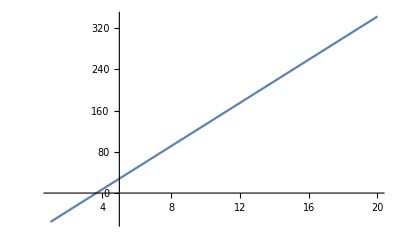

```mathematica
plotfitdata1 = Plot[fitdata1,{x,1,20}]
```

## 合并这些图形

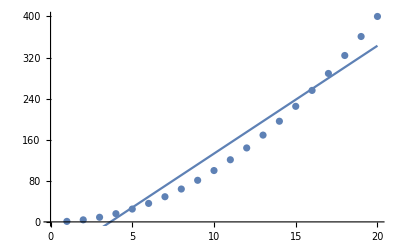

```mathematica
Show[lpdata1,plotfitdata1]
```